# Lab 4 Example

Get the current directory.

```mathematica
dir = NotebookDirectory[];
```

```mathematica
SetDirectory[dir];
```

Import sample crater data to fit [x, y, sigma].

```mathematica
data = Import[dir <> "ca7.txt", "Table"];
```

Function to Linearly Solve a a polynomial system. Takes a list of xs, ys, the sigma accuracies, and a number M that represents the order of the polynomial we are solving for.

```mathematica
linSolve[xvals_, yvals_, sig_, M_] := Module[
	{A = Table[xvals[[i]]^(j-1)/sig[[i]], {i, Length[xvals]},{j, M}], 
	beta = Table[yvals[[i]]/sig[[i]], {i, Length[yvals]}]},
LinearSolve[Transpose[A].A,Transpose[A]. beta]];
```

```mathematica
xs = data[[All, 1]];
```

```mathematica
ys = data[[All, 2]];
```

```mathematica
sig = data[[All, 3]];
```

Solve for the fit.

```mathematica
fit =  linSolve[xs, ys, sig, 3]
```

{1.10936,-30.0942,5.01466}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
func = Plus@@Table[x^(i-1) * fit[[i]], {i, Length[fit]}]
```

1.10936-30.0942 x+5.01466 x^2

Plot the data with the found function.

```mathematica
plotData3B = Transpose[{Transpose[{xs,ys}],Map[Function[x,ErrorBar[x]], sig]}];
```

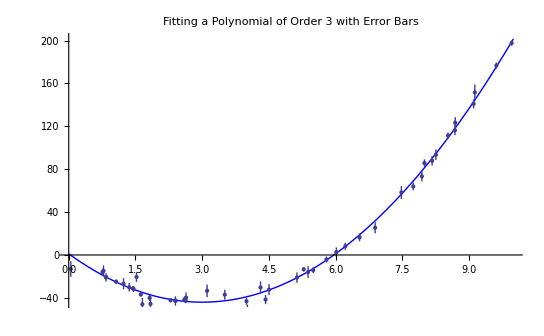

```mathematica
Show[Plot[func, {x, 0 , 10}, PlotStyle -> {Blue}], ErrorListPlot[plotData3B],PlotLabel -> "Fitting a Polynomial of Order 3 with Error Bars"]
```

```mathematica
A = Table[xs[[i]]^(j-1)/ sig[[i]], {i, Length[xs]},{j, 3}];
```

Get the covariance matrix.

```mathematica
cov = Inverse[Transpose[A].A]
```

{{0.120211,-0.153102,0.0168061},{-0.153102,0.198357,-0.0219573},{0.0168061,-0.0219573,0.00258338}}

Calculate a space of random lines to see the space of likely lines to approximate the 95% confidence.

```mathematica
otherLines = RandomVariate[MultinormalDistribution[fit, cov],500];
```

```mathematica
otherFuncs = Map[Function[fit,Plus@@Table[x^(i-1) * fit[[i]], {i, Length[fit]}]], otherLines];
```

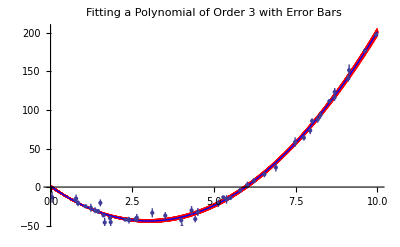

```mathematica
Show[Plot[otherFuncs, {x,0,10}, PlotStyle -> Red],Plot[func, {x, 0 , 10}, PlotStyle -> {Blue}], ErrorListPlot[plotData3B],PlotLabel -> "Fitting a Polynomial of Order 3 with Error Bars"]
```